# Schur Transform

The general idea behind this algorithm is to implement the Schur Transform recursively, through applying a direct sum of relevant CG transforms for irreps of a Schur basis of n qubits to a Tensor product of a Schur Transform for n qubits and a 2x2 Identity matrix (this tensor product with identity represents adding a new qubit), thus obtaining something like a Schur Transform for n+1 qubits, although with certain rows disordered. We then have to apply a certain permutation matrix in order to obtain the true Schur Transform for n+1 qubits.
The CG transform, when acting on an irrep of dimensionality d of n-qubit Schur basis, outputs two irreps of n+1-qubit Schur basis, one of them with dimensionality d+1 and the other with dimensionality d-1.

```mathematica
(*Identity matrix of size d×d*)
Id[d_]:=SparseArray[Band[{1,1}]->1,{d,d}];
```

## CG

In this step we implement the Clebsch-Gordan (CG) transform for a subspace (irrep) of dimension d.
We do that directly, by making a sparse array with non-zero values being the CG-coefficients at specific corresponding positions in the matrix.

```mathematica
(*Parameters:*)(*l=2j=overhang*)(*w=j-m=Hamming weight of the overhang∈[0,l]*)(*Example:when j=1/2 we have:m=1/2-> |0>and m=-(1/2)-> |1>*)(*Δl∈{-1,+1} change in overhang*)(*x∈{0,1} the new symbol*)MyCG[l_,w_,Δl_,x_]:=If[x==0,Δl,1] 1/Sqrt[2] Sqrt[(l+1+Δl(1-2 x)(l+1-2 (w+x)))/(l+1)];
CG[d_]:=Module[{l1,l2,l3,l4},(*Increase overhang*)l1=Table[{i+1,2i}->MyCG[d-1,i-1,1,1],{i,1,d}];
l2=Table[{i+1,2i+1}->MyCG[d-1,i,1,0],{i,0,d-1}];
(*Decrease overhang*)l3=Table[{(d+1)+i+1,2i+2}->MyCG[d-1,i,-1,1],{i,0,d-2}];
l4=Table[{(d+1)+i+1,2i+2+1}->MyCG[d-1,i+1,-1,0],{i,0,d-2}];
SparseArray[Join[l1,l2,l3,l4],{2d,2d}]];
```

```mathematica
DirectSum[lst_]:=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@lst];
```

## Auxiliary functions for implementing the Schur Basis

In this step we implement a depiction of the Schur Basis that uniquely defines every independent basis state. This depiction is equivalent to the classic one, which consists of three main components: partition, Standard Young Tableux (SYT) and the Semi-Standard Young Tableau (SSYT). 
We also define some auxiliary functions that help to manipulate and construct new basis elements for higher number of qubits from lower number of qubits (specifically, by adding one qubit).

```mathematica
SchurBasis0 = {{{0,1},{1},{},{0}},{{0,1},{1},{},{1}}} (*This is the depiction of Schur basis for one qubit. Every element on the first level is a basis element. Inside every basis element, so on the second level, there are four elements: 
-first represents the partition, where the first element in the partition is the number of boxes (elements) in the second row of SYT (and SSYT) and the second 
element is the number of boxes in the first row of SYT (and SSYT) (for example: {2,4} means there are 2 boxes in second row of SYT and 4 in the first);
  -second represents the first row of SYT, with its elements being the numbers in boxes of the first row of SYT (in order);
  -third represents the second row of SYT, with its elements being the numbers in boxes of the second row of SYT (in order, shares order with the first row);
(* Example for second and third: {1,2,4},{3,5} means that the first two qubits have their total spin (total angular momentum) added (1,2 in first row), for the third qubit the total spin (1/2 for one qubit) is subtracted from the total spin of the system (i.e. J3 = J2 - 1/2; 3 in the second row), the total spin of fourth qubit was added (4 in first) and total spin of fifth qubit was subtracted (5 in second) *)
  -fourth represents the Hamming weight of the overhang, which, given a partition, uniquely determines the SSYT.*)
```

{{{0,1},{1},{},{0}},{{0,1},{1},{},{1}}}

```mathematica
NumSSYT[n_, l2_]:=n-2*l2+1; (* Function of total number of boxes (qubits) 'n' in SSYT and the number of boxes in the second row 'l2', computes the number of SSYT's with these parameters. *)
```

```mathematica
NumSYT[n_,l2_]:= Binomial[n+1,l2]*(n-2*l2+1)/(n+1); (* Function of total number of boxes (qubits) 'n' in SYT and the number of boxes in the second row 'l2', computes the number of SYT's with these parameters. *)
```

```mathematica
AddFirst0[a_]:=(ReplacePart[a, {{1,2}->(a[[1,2]]+1), {2}->Join[a[[2]],{a[[1,1]]+a[[1,2]]+1}]}]); (* Supporting function for AddFirst, represents adding a box (qubit) to the first row of the Young Tableau for a given basis element 'a', thus increasing the second entry in partition by one i.e. increasing the number of elements in the first row and adding a number that is next in order to the SYT first row entry, i.e. for an SYT of {1,2,4} {3,5} it adds 6 to the first row entry turning the SYT into {1,2,4,6} {3,5} *)
```

```mathematica
AddFirst[a_]:= Module[{x},x=Map[AddFirst0,a];x=ReplacePart[x, {-1}->Sequence[x[[-1]],x[[-1]]]];x[[-1,4,1]]++;Return[x]]; (* Adds a box (qubit) to the first row for every basis element in a given set 'a' i.e. applies AddFirst0 to every basis element in a given set and then adds a new basis element to the set with max Hamming weight increased by one because the number of SSYT's gets increased by one *)
```

```mathematica
AddSecond0[a_]:=(ReplacePart[a, {{1,1}->(a[[1,1]]+1), {3}->Join[a[[3]],{a[[1,1]]+a[[1,2]]+1}]}]); (* Supporting function for AddSecond, represents adding a box (qubit) to the second row of the Young Tableau for a given basis element 'a', thus increasing the first entry in partition by one i.e. increasing the number of elements in the second row and adding a number that is next in order to the SYT second row entry, i.e. for an SYT of {1,2,4} {3,5} it adds 6 to the second row entry turning the SYT into {1,2,4} {3,5,6} *)
```

```mathematica
AddSecond[a_]:= Module[{x},x=Map[AddSecond0,a];x= Delete[x,-1]]; (* Adds a box (qubit) to the second row for every basis element in a given set 'a' i.e. applies AddSecond0 to every basis element in a given set and then deletes the last basis element in this set because the number of SSYT's gets decreased by one *)
```

## Permutation for CG

This step is more for the showcase of this important part in the algorithm, because afterwards the Permutation function is merged with the CG recursion step to form the Schur Transform, as this way the implementation is faster.
This part computes the permutation matrix that we have to apply after the CG recursive step. This permutation is needed because the CG recursion outputs a direct sum of all higher and lower irreps in order in n+1 qubit space for every irrep in n qubit space. So, for example, for a direct sum of irreps (ir1, ir2, ir3) in this order it would output a direct sum of irreps (Higher[ir1], Lower[ir1], Higher[ir2], Lower[ir2], Higher[ir3], Lower[ir3]) in this order, but this is not necessarily the correct order in which the Schur Transform should order the irreps (or blocks, if applied to matrices). Say, if (ir1, ir2, ir3) have dimensions (6, 4, 4) respectively, the output would have dimensions (7, 5, 5, 3, 5, 3) in this order, while the actual order should have been: (7, 5, 5, 5, 3, 3).
This step utilizes the Schur Basis depiction introduced earlier in order to modify the basis in the same way the CG recursion step does and obtain a basis for a higher number of qubits, but disordered in the same way as the result of the CG recursion step. We then apply Ordering to the disordered Schur Basis depiction and obtain a permutation vector, that essentially gives us the needed permutation to get the true Schur Transform.

```mathematica
Permutation[n_]:=  Module[{counter,subsp,ar,sb,num,first,second},
sb=SchurBasis0; (* Schur basis for 1 qubit *)
num=1; (* Iterator for the number of qubits *)
While[num<n, (* Cycle goes through all Schur Basis depictions until n, recursive nature to replicate what happens to basis in CG recursion step *)
sb = Sort[sb]; (* Sort at the start of each cycle so that we can get an unsorted Schur Basis depiction when While ends *)
ar={}; (* Auxiliary array that helps to update sb at every cycle *)
counter = 1;
For[l2=0,l2<=Quotient[num,2],l2++, (* Starts with all boxes in first row, adds one box to second until max possible amount reached, thus going through all dimensions of irreps *)
For[j=1,j<=NumSYT[num,l2],j++, (* Goes through all possible SYT's for a given dimension for irrep, keeps track of multiplicity for each irrep, i.e. repeats the cycle as many times as the multiplicity of an irrep of given dimensionality *)
subsp = sb[[counter;;counter+NumSSYT[num,l2]-1]]; (* Gets an irrep (spin subspace) from sb *)
first = AddFirst[subsp]; (* Adds box to first row for every basis element in an irrep *)
second = AddSecond[subsp]; (* Adds box to second row for every basis element in an irrep *)
subsp = Join[first,second]; (* Gives a joined subspace of two new irreps -- higher (AddFirst) and lower (AddSecond) *)
ar = Join[ar,subsp]; (* Step by step builds the new (disordered!) Schur Basis *)
counter = counter + NumSSYT[num,l2] (* Goes to position of the next irrep *)
]
];
sb = ar; (* Set the old Schur Basis to the new one with one more qubit *)
num++; (* Goes to the subspace with one more qubit *)
];
Return[Ordering[sb]] (* Returns the ordering for the final unsorted sb *)
]
```

## Schur Transform through CG and Permutation

In this step we implement the Schur Transform itself by combining CG recursion and Permutation.  It’s natural to combine these two parts of the algorithm as they exist within the same recursion.
Everything is implemented through Sparse Arrays to make it faster.

```mathematica
SchurTransform[n_]:= Module[{counter,subsp,ar,sb,num,first,second,SchurTrans,ClebGor},
sb=SchurBasis0;
num=1;
SchurTrans= SparseArray[IdentityMatrix[2]]; (* Schur Transform for 1 qubit *)
While[num<n,
sb = Sort[sb];
ar={};
counter = 1; (* Taken from Permutation up to this point *)
ClebGor=SparseArray[CG[NumSSYT[num,0]]]; (* The first CG in direct sum with the highest dimensionality for the irrep, i.e. all boxes in first row *)
For[l2=0,l2<=Quotient[num,2],l2++,
For[j=1,j<=NumSYT[num,l2],j++,
subsp = sb[[counter;;counter+NumSSYT[num,l2]-1]];
first = AddFirst[subsp];
second = AddSecond[subsp];
subsp = Join[first,second];
ar = Join[ar,subsp];
counter = counter + NumSSYT[num,l2]; (* Taken from Permutation up to this point *)
If[l2==0,Continue[], (* Continue so that to skip the direct sum for the first CG, which was already set above *)
ClebGor=ArrayFlatten[{{ClebGor,0},{0,SparseArray[CG[NumSSYT[num,l2]]]}}]] (* Append to ClebGor the direct sum of ClebGor with the CG for the next irrep, thus constructing the total direct sum of relevant CG's *)
]
];
sb = ar;
num++; (* Taken from Permutation up to this point *)
SchurTrans = PermutationMatrix[Ordering[sb]].ClebGor.KroneckerProduct[SchurTrans, SparseArray[IdentityMatrix[2]]] (* Construct the new Schur Transform from the old one, using the product of the direct sum of CG's with the Tensor product of the Schur Transform with Identity (representing adding one more qubit) and multiplying everything by the Permutation Matrix from the left *)
];
Return[SchurTrans]
]
```

## Workspace

```mathematica
(* TensMat is U2Mat tensored with itself m times *)
U2Mat = {{a,b},{c,d}};
m := 8; (* Change m here, if needed *)
For[i=1; TensMat = U2Mat, i< m, i++, TensMat = KroneckerProduct[TensMat,U2Mat]];
```

```mathematica
TensMat // MatrixForm;
```

```mathematica
(* GenSwap[k,n] is a permutation matrix that permutes k and k+1 qubits in a system of n qubits *)
Swap = {{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}};
GenSwap[k_,n_]:=Module[{PerMat},
     For[i=1;PerMat=Swap,i<k,i++,PerMat=KroneckerProduct[IdentityMatrix[2],PerMat]];
For[i=k,i<n-1,i++,PerMat=KroneckerProduct[PerMat,IdentityMatrix[2]]];
Return[PerMat];
]
```

```mathematica
GenSwap[2,4] // MatrixForm;
```

```mathematica
(* General Clebsch Gordan transform for size 16 x 16, transforming two previous systems in the binary tree, i.e. for j1=1,0 and j2=1,0 into J=2,1,0 *)
Off[ClebschGordan::phy]
cg1=Join@@Table[Transpose@Flatten[Table[ClebschGordan[{1,m1},{1,m2},{J,m}],{m1,-1,1},{m2,-1,1},{m,-J,J}],{{1,2},{3}}],{J,2,0,-1}];
cg2=Join@@Table[Transpose@Flatten[Table[ClebschGordan[{1,m1},{0,m2},{J,m}],{m1,-1,1},{m2,0,0},{m,-J,J}],{{1,2},{3}}],{J,1,1,-1}];
cg3=Join@@Table[Transpose@Flatten[Table[ClebschGordan[{0,m1},{1,m2},{J,m}],{m1,0,0},{m2,-1,1},{m,-J,J}],{{1,2},{3}}],{J,1,1,-1}];
cg4=Join@@Table[Transpose@Flatten[Table[ClebschGordan[{0,m1},{0,m2},{J,m}],{m1,0,0},{m2,0,0},{m,-J,J}],{{1,2},{3}}],{J,0,0,-1}];
AlmostGCG = DirectSum[{cg1,cg2,cg3,cg4}];
PermutMat=PermutationMatrix[{1,2,3,5,6,7,9,10,11,4,8,12,13,14,15,16}];
FinalPermutMat=PermutationMatrix[{1,2,3,4,5,6,7,8,10,11,12,13,14,15,9,16}];
GCG = FinalPermutMat.AlmostGCG.PermutMat;
```

```mathematica
(* General Clebsch Gordan transform for size 256 x 256, transforming two previous systems in the binary tree, i.e. for j1=2,1,0 and j2=2,1,0 into J=4,3,2,1,0 *)

(* All the used coefficients: *)
cg22=Join@@Table[Transpose@Flatten[Table[ClebschGordan[{2,m1},{2,m2},{J,m}],{m1,-2,2},{m2,-2,2},{m,-J,J}],{{1,2},{3}}],{J,4,0,-1}];
cg21=Join@@Table[Transpose@Flatten[Table[ClebschGordan[{2,m1},{1,m2},{J,m}],{m1,-2,2},{m2,-1,1},{m,-J,J}],{{1,2},{3}}],{J,3,1,-1}];
cg20=Join@@Table[Transpose@Flatten[Table[ClebschGordan[{2,m1},{0,m2},{J,m}],{m1,-2,2},{m2,0,0},{m,-J,J}],{{1,2},{3}}],{J,2,2,-1}];
cg12=Join@@Table[Transpose@Flatten[Table[ClebschGordan[{1,m1},{2,m2},{J,m}],{m1,-1,1},{m2,-2,2},{m,-J,J}],{{1,2},{3}}],{J,3,1,-1}];
cg11=Join@@Table[Transpose@Flatten[Table[ClebschGordan[{1,m1},{1,m2},{J,m}],{m1,-1,1},{m2,-1,1},{m,-J,J}],{{1,2},{3}}],{J,2,0,-1}];
cg10=Join@@Table[Transpose@Flatten[Table[ClebschGordan[{1,m1},{0,m2},{J,m}],{m1,-1,1},{m2,0,0},{m,-J,J}],{{1,2},{3}}],{J,1,1,-1}];
cg02=Join@@Table[Transpose@Flatten[Table[ClebschGordan[{0,m1},{2,m2},{J,m}],{m1,0,0},{m2,-2,2},{m,-J,J}],{{1,2},{3}}],{J,2,2,-1}];
cg01=Join@@Table[Transpose@Flatten[Table[ClebschGordan[{0,m1},{1,m2},{J,m}],{m1,0,0},{m2,-1,1},{m,-J,J}],{{1,2},{3}}],{J,1,1,-1}];
cg00=Join@@Table[Transpose@Flatten[Table[ClebschGordan[{0,m1},{0,m2},{J,m}],{m1,0,0},{m2,0,0},{m,-J,J}],{{1,2},{3}}],{J,0,0,-1}];
(* Permutation of registers A⊗B into B⊗A *)
BigPermutation[da_,db_]:=PermutationMatrix[Join@@Table[j*db+i,{i,1,db},{j,0,da-1}]];
(* Direct sum of permutations of registers *)
AlmostPermutation8=DirectSum[{BigPermutation[5,16],BigPermutation[9,16],BigPermutation[2,16]}];
(* Move all the multiplicities (Identity matrices) to the leftmost positions *)
Permutation8=DirectSum[{IdentityMatrix[80],KroneckerProduct[BigPermutation[5,3],IdentityMatrix[3]],KroneckerProduct[IdentityMatrix[3],BigPermutation[3,3],IdentityMatrix[3]],KroneckerProduct[IdentityMatrix[2],BigPermutation[1,3],IdentityMatrix[3]],KroneckerProduct[BigPermutation[5,2],IdentityMatrix[1]],KroneckerProduct[IdentityMatrix[3],BigPermutation[3,2],IdentityMatrix[1]],KroneckerProduct[IdentityMatrix[2],BigPermutation[1,2],IdentityMatrix[1]]}];
(* Combine the two permutations *)
Permutation8=Permutation8.AlmostPermutation8;
(* Direct sum of CG's in appropriate order (remember changed registers) *)
AlmostGCG8=DirectSum[{cg22,cg12,cg12,cg12,cg02,cg02,cg21,cg21,cg21,cg11,cg11,cg11,cg11,cg11,cg11,cg11,cg11,cg11,cg01,cg01,cg01,cg01,cg01,cg01,cg20,cg20,cg10,cg10,cg10,cg10,cg10,cg10,cg00,cg00,cg00,cg00}];
(* Take permutation into account *)
GCG8=AlmostGCG8.Permutation8;
```

```mathematica
(*!!!*)
(* Note: We still lack the final permutation for GCG8 after applying the direct sum of cg's to the permuted tensor product. We are dealing with this permutation later below *)
(*!!!*)
```

```mathematica
(* Make Schur Transforms for the whole tree recursively combining previous Schur's *)
(* 4 qubits *)
GCGSchur= GCG.KroneckerProduct[SchurTransform[2],SchurTransform[2]];
(* 8 qubits *)
GCGSchur8=GCG8.KroneckerProduct[GCGSchur,GCGSchur];
```

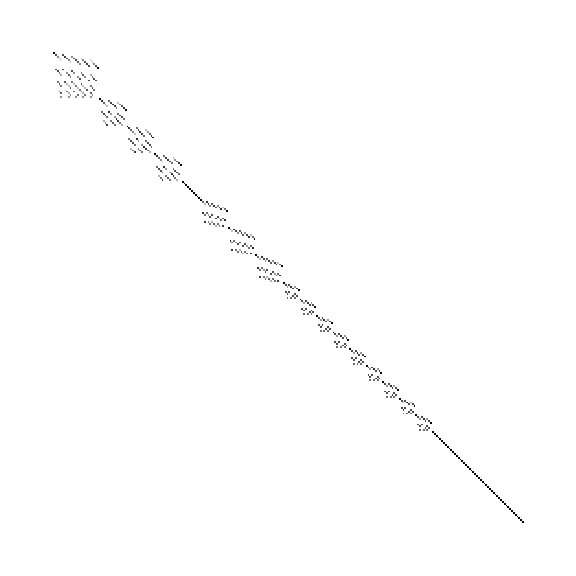
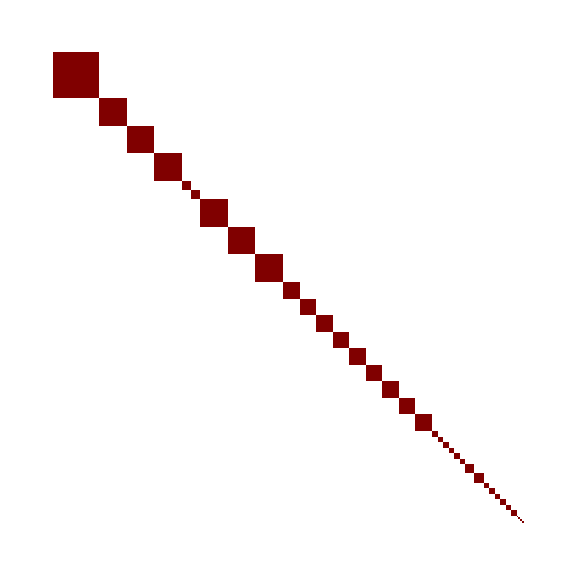
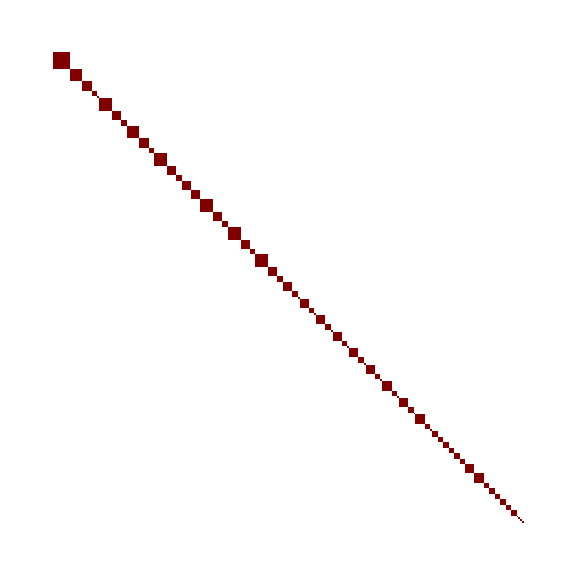

```mathematica
(* Check that the direct sum of cg's for 8 qubits is applied to the correct blocks (i.e. that the blocks before application are in correct order) *)
Mat=SchurTransform[2].KroneckerProduct[U2Mat,U2Mat].ConjugateTranspose[SchurTransform[2]] // FullSimplify;
Mat=KroneckerProduct[Mat,Mat];
TransfMat=GCG.Mat.GCG†// FullSimplify;
Matrr=Permutation8.KroneckerProduct[TransfMat,TransfMat].Permutation8ᵀ;
ArrayPlot[#,ImageSize->Large]&/@{AlmostGCG8,Matrr,Simplify[AlmostGCG8.Matrr.AlmostGCG8ᵀ]}
```

```mathematica
(* Check unitarity *)
SparseArray[GCGSchur8];
%.%ᵀ==IdentityMatrix[256]
```

True

```mathematica
(* Now, dealing with the last permutation: *)
```

```mathematica
(* Create an almost transformed TensMat for 8 qubits and turn it into block diagonal matrix *)
AlmostTransfTensMat8=Simplify[SparseArray[GCGSchur8].TensMat.SparseArray[GCGSchur8ᵀ]];
BlockMat=BlockDiagonalMatrix[AlmostTransfTensMat8];
Blocks=BlockMat["Blocks"];
(* Sort the blocks highest dimension to lowest and achieve a transformed TensMat *)
TransfTensMat8=BlockDiagonalMatrix@Reverse[Blocks[[Ordering[Length/@Blocks]]]];
```

```mathematica
(* Create two ordering vectors for diagonal elements of both transformed and almost transformed matrix, they both achieve the same result after sorting according to them *)
v1=Ordering[Diagonal[AlmostTransfTensMat8]];
v2=Ordering[Diagonal[TransfTensMat8]];
(* The final permutation would be first sorting according to v1, then unsorting according to v2 *)
FinalPermutation=PermutationMatrix[v2]ᵀ.PermutationMatrix[v1];
```

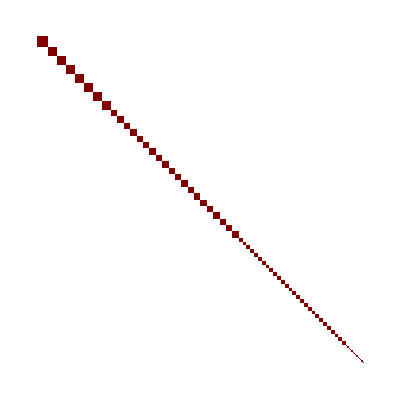

```mathematica
(* Check that this works *)
FinalPermutation.AlmostTransfTensMat8.FinalPermutationᵀ // ArrayPlot
```

```mathematica
(* Create an almost transformed GenSwap of 4th and 5th qubits for 8 qubits *)
AlmostTransfGenSwap48=Simplify[SparseArray[GCGSchur8].GenSwap[4,8].SparseArray[GCGSchur8ᵀ]];
```

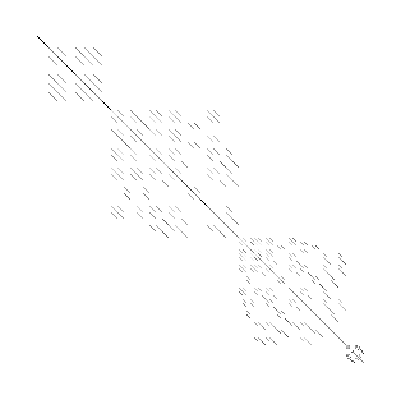

```mathematica
(* Finish the transformation according to the Final Permutation *)
TransfGenSwap48= FinalPermutation.AlmostTransfGenSwap48.FinalPermutationᵀ ;
TransfGenSwap48// ArrayPlot
```

```mathematica
(* Analyze the blocks of GenSwap of 4th and 5th qubits for 8 qubits *)
BlockMatrix48=BlockDiagonalMatrix[TransfGenSwap48];
Union@BlockMatrix48["Blocks"];
MatrixForm/@%
Eigenvalues/@%%
```

{(1),(-1/2 | (√3)/2
(√3)/2 | 1/2),(0 | -1/(√2) | -1/(√2)
-1/(√2) | 1/2 | -1/2
-1/(√2) | -1/2 | 1/2),(0 | 1/(√2) | 1/(√2)
1/(√2) | 1/2 | -1/2
1/(√2) | -1/2 | 1/2),(1/4 | (√(3/2))/2 | -(√3)/4 | (√(3/2))/2
(√(3/2))/2 | 1/2 | 1/(2 √2) | -1/2
-(√3)/4 | 1/(2 √2) | 3/4 | 1/(2 √2)
(√(3/2))/2 | -1/2 | 1/(2 √2) | 1/2),(1/4 | -(√3)/4 | (√(3/2))/2 | (√(3/2))/2
-(√3)/4 | 3/4 | 1/(2 √2) | 1/(2 √2)
(√(3/2))/2 | 1/(2 √2) | 1/2 | -1/2
(√(3/2))/2 | 1/(2 √2) | -1/2 | 1/2),(1/2 | -1/(2 √2) | 1/2 | -1/(2 √2) | 1/2
-1/(2 √2) | 3/4 | 1/(2 √2) | -1/4 | 1/(2 √2)
1/2 | 1/(2 √2) | 1/2 | 1/(2 √2) | -1/2
-1/(2 √2) | -1/4 | 1/(2 √2) | 3/4 | 1/(2 √2)
1/2 | 1/(2 √2) | -1/2 | 1/(2 √2) | 1/2),(-1/4 | -(√(5/3))/4 | (√(5/6))/2 | 0 | -(√(5/6))/2 | (√(5/3))/2
-(√(5/3))/4 | 1/4 | -1/(2 √2) | -1/(√3) | 1/(2 √2) | 1/2
(√(5/6))/2 | -1/(2 √2) | 1/2 | -1/(√6) | 1/2 | 0
0 | -1/(√3) | -1/(√6) | 1/2 | 1/(√6) | 1/(2 √3)
-(√(5/6))/2 | 1/(2 √2) | 1/2 | 1/(√6) | 1/2 | 0
(√(5/3))/2 | 1/2 | 0 | 1/(2 √3) | 0 | 1/2),(-1/4 | -(√(5/3))/4 | (√(5/6))/2 | -(√(5/6))/2 | (√(5/3))/2 | 0
-(√(5/3))/4 | 1/4 | -1/(2 √2) | 1/(2 √2) | 1/2 | -1/(√3)
(√(5/6))/2 | -1/(2 √2) | 1/2 | 1/2 | 0 | -1/(√6)
-(√(5/6))/2 | 1/(2 √2) | 1/2 | 1/2 | 0 | 1/(√6)
(√(5/3))/2 | 1/2 | 0 | 0 | 1/2 | 1/(2 √3)
0 | -1/(√3) | -1/(√6) | 1/(√6) | 1/(2 √3) | 1/2),(-1/4 | (√(5/3))/4 | -(√(5/6))/2 | -(√(5/6))/2 | (√(5/3))/2 | 0
(√(5/3))/4 | 1/4 | -1/(2 √2) | -1/(2 √2) | -1/2 | 1/(√3)
-(√(5/6))/2 | -1/(2 √2) | 1/2 | -1/2 | 0 | 1/(√6)
-(√(5/6))/2 | -1/(2 √2) | -1/2 | 1/2 | 0 | 1/(√6)
(√(5/3))/2 | -1/2 | 0 | 0 | 1/2 | 1/(2 √3)
0 | 1/(√3) | 1/(√6) | 1/(√6) | 1/(2 √3) | 1/2),(1/8 | -(√7)/8 | (√(7/2))/4 | 0 | -(√7)/8 | (√(7/2))/4 | (√(7/3))/8 | -(√(7/6))/4 | -(√(7/6))/4 | (√(7/3))/4 | 0
-(√7)/8 | 3/8 | -1/(4 √2) | -1/2 | -1/8 | 1/(4 √2) | -(√3)/8 | (√(3/2))/4 | -(√(3/2))/4 | (√3)/4 | 0
(√(7/2))/4 | -1/(4 √2) | 1/2 | -1/(2 √2) | 1/(4 √2) | -1/4 | -(√(3/2))/4 | (√3)/4 | 0 | 0 | 0
0 | -1/2 | -1/(2 √2) | 1/2 | 0 | 0 | -1/(2 √3) | 1/(√6) | -1/(2 √6) | 1/(2 √3) | 0
-(√7)/8 | -1/8 | 1/(4 √2) | 0 | 3/8 | -1/(4 √2) | -(√3)/8 | -(√(3/2))/4 | (√(3/2))/4 | (√3)/4 | -1/2
(√(7/2))/4 | 1/(4 √2) | -1/4 | 0 | -1/(4 √2) | 1/2 | -(√(3/2))/4 | 0 | (√3)/4 | 0 | -1/(2 √2)
(√(7/3))/8 | -(√3)/8 | -(√(3/2))/4 | -1/(2 √3) | -(√3)/8 | -(√(3/2))/4 | 5/8 | 1/(4 √2) | 1/(4 √2) | 1/4 | -1/(2 √3)
-(√(7/6))/4 | (√(3/2))/4 | (√3)/4 | 1/(√6) | -(√(3/2))/4 | 0 | 1/(4 √2) | 1/2 | 1/4 | 0 | -1/(2 √6)
-(√(7/6))/4 | -(√(3/2))/4 | 0 | -1/(2 √6) | (√(3/2))/4 | (√3)/4 | 1/(4 √2) | 1/4 | 1/2 | 0 | 1/(√6)
(√(7/3))/4 | (√3)/4 | 0 | 1/(2 √3) | (√3)/4 | 0 | 1/4 | 0 | 0 | 1/2 | 1/(2 √3)
0 | 0 | 0 | 0 | -1/2 | -1/(2 √2) | -1/(2 √3) | -1/(2 √6) | 1/(√6) | 1/(2 √3) | 1/2),(-1/8 | -(√3)/8 | (√(3/2))/4 | -(√3)/8 | (√(3/2))/4 | (√5)/8 | -(√(5/2))/4 | -(√(5/2))/4 | (√5)/4 | 0 | 0 | 0 | 0
-(√3)/8 | 1/8 | -3/(4 √2) | -1/24 | 1/(12 √2) | -(√(5/3))/8 | (√(5/6))/4 | -(√(5/6))/4 | (√(5/3))/4 | (√5)/6 | -(√(5/2))/3 | 0 | 0
(√(3/2))/4 | -3/(4 √2) | 1/2 | 1/(12 √2) | -1/12 | -(√(5/6))/4 | (√(5/3))/4 | 0 | 0 | (√(5/2))/6 | -(√5)/6 | 0 | 0
-(√3)/8 | -1/24 | 1/(12 √2) | 1/8 | -3/(4 √2) | -(√(5/3))/8 | -(√(5/6))/4 | (√(5/6))/4 | (√(5/3))/4 | 0 | 0 | (√5)/6 | -(√(5/2))/3
(√(3/2))/4 | 1/(12 √2) | -1/12 | -3/(4 √2) | 1/2 | -(√(5/6))/4 | 0 | (√(5/3))/4 | 0 | 0 | 0 | (√(5/2))/6 | -(√5)/6
(√5)/8 | -(√(5/3))/8 | -(√(5/6))/4 | -(√(5/3))/8 | -(√(5/6))/4 | 3/8 | -1/(4 √2) | -1/(4 √2) | -1/4 | -1/(2 √3) | -1/(√6) | -1/(2 √3) | -1/(√6)
-(√(5/2))/4 | (√(5/6))/4 | (√(5/3))/4 | -(√(5/6))/4 | 0 | -1/(4 √2) | 1/2 | -1/4 | 0 | -1/(√6) | 0 | -1/(2 √6) | -1/(2 √3)
-(√(5/2))/4 | -(√(5/6))/4 | 0 | (√(5/6))/4 | (√(5/3))/4 | -1/(4 √2) | -1/4 | 1/2 | 0 | -1/(2 √6) | -1/(2 √3) | -1/(√6) | 0
(√5)/4 | (√(5/3))/4 | 0 | (√(5/3))/4 | 0 | -1/4 | 0 | 0 | 1/2 | -1/(2 √3) | 0 | -1/(2 √3) | 0
0 | (√5)/6 | (√(5/2))/6 | 0 | 0 | -1/(2 √3) | -1/(√6) | -1/(2 √6) | -1/(2 √3) | 1/2 | 0 | -1/3 | -1/(3 √2)
0 | -(√(5/2))/3 | -(√5)/6 | 0 | 0 | -1/(√6) | 0 | -1/(2 √3) | 0 | 0 | 1/2 | -1/(3 √2) | -1/6
0 | 0 | 0 | (√5)/6 | (√(5/2))/6 | -1/(2 √3) | -1/(2 √6) | -1/(√6) | -1/(2 √3) | -1/3 | -1/(3 √2) | 1/2 | 0
0 | 0 | 0 | -(√(5/2))/3 | -(√5)/6 | -1/(√6) | -1/(2 √3) | 0 | 0 | -1/(3 √2) | -1/6 | 0 | 1/2)}

{{1},{-1,1},{-1,1,1},{-1,1,1},{-1,1,1,1},{-1,1,1,1},{-1,1,1,1,1},{-1,-1,1,1,1,1},{-1,-1,1,1,1,1},{-1,-1,1,1,1,1},{-1,-1,-1,1,1,1,1,1,1,1,1},{-1,-1,-1,-1,1,1,1,1,1,1,1,1,1}}